```mathematica
ClearAll["Global`*"]
```

```mathematica
f[n_, k_, a_] := f[n,k,a]=Sum[ f[n/(a+j), k-1, a],{j,0,Floor[n-a]}]; f[n_, 0, a_]:=1
```

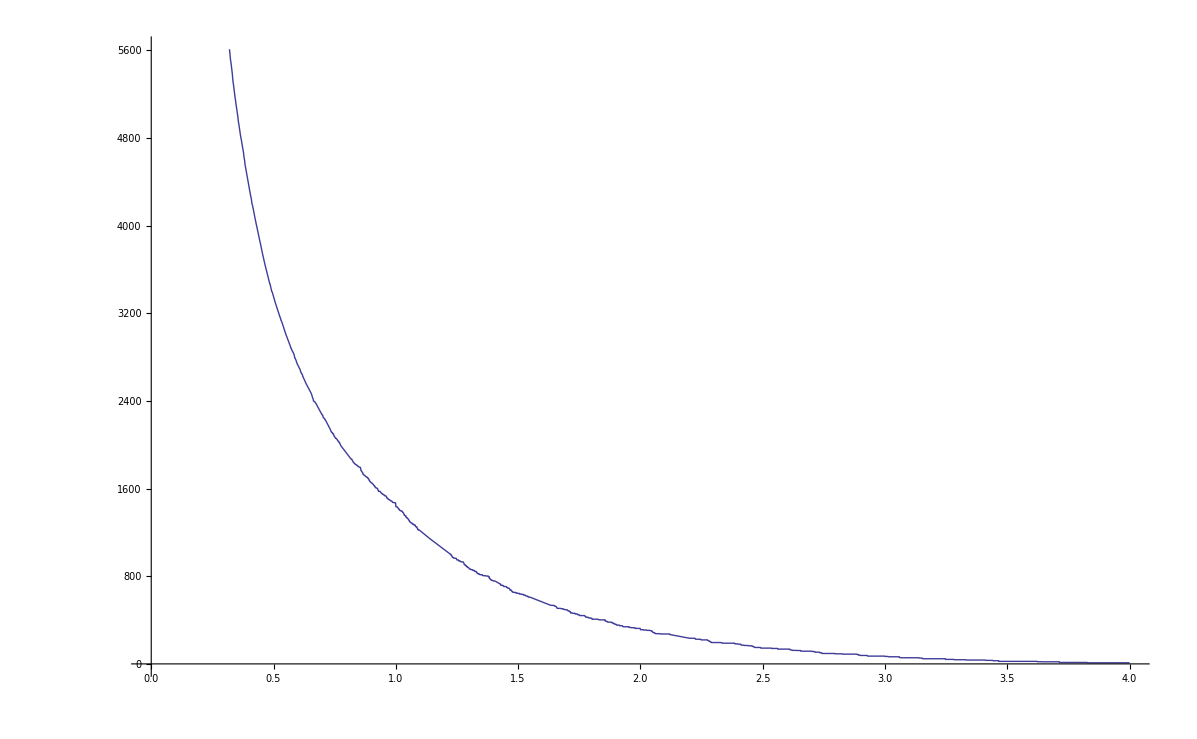

```mathematica
Plot[f[100,3,a],{a,0,4}]
```

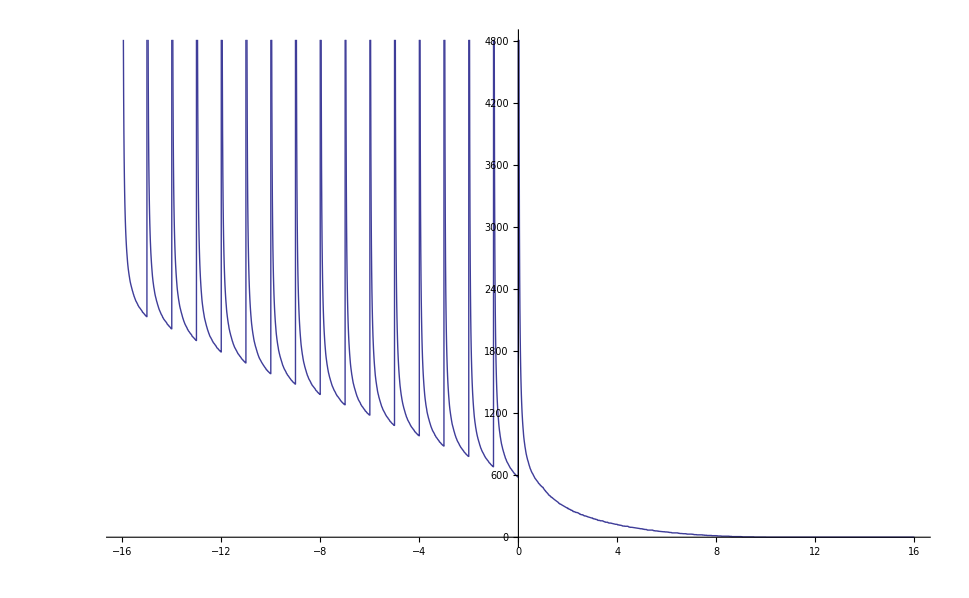

```mathematica
Plot[f[100,2,a],{a,-16,16}]
```

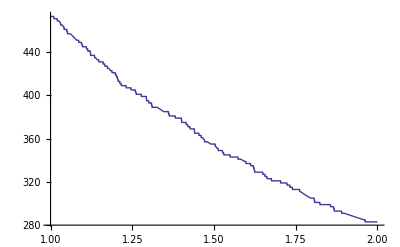

```mathematica
Plot[f[100,2,a],{a,1,2}]
```

```mathematica
f[100,2,11]
```

0

```mathematica
Dhyp[n_,k_,a_]:=Sum[Binomial[k,j] Dhyp[Floor[n/(m^(k-j))],j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
Dhyp[n_,1,a_]:=Floor[n]-a+1;Dhyp[n_,0,a_]:=1
```

```mathematica
24^-2 f[100 24^2,3,25]
```

4493/144

```mathematica
24^-2 Dhyp[100 24^2,3,25]
```

4493/144

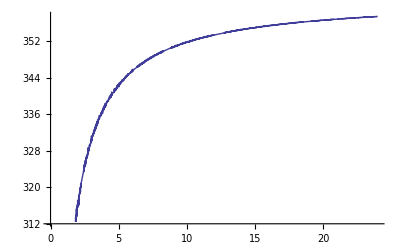

```mathematica
Plot[n^-2 Dhyp[100 n^2, 2, n+1],{n,0,24}]
```

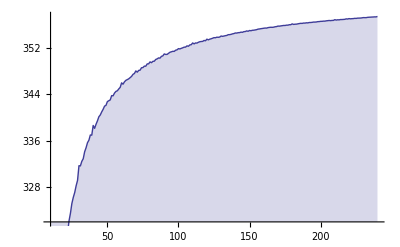

```mathematica
DiscretePlot[(n*.1)^-2 f[100 (n*.1)^2, 2, (n*.1)+1],{n,10,240}]
```

```mathematica
N[Gamma[2,0,-Log[100]]/Gamma[2]]
```

361.517-4.41506×10^-14 ⅈ

```mathematica
f[100,2,k]
```

∑_(j=0)^(100+Floor[-k]) (1+Floor[(100-j k-k^2)/(j+k)])

```mathematica
f2[k_] := k^-2 f[10 k^2,2,k+1]
```

```mathematica
f2'[4]
```

General::ivar: 4 is not a valid variable.

-2351/32+(∂_4 2351)/16

General::ivar: 3 is not a valid variable.

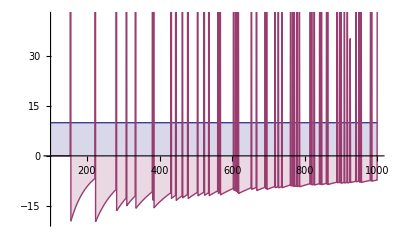

```mathematica
DiscretePlot[ {10, (f2[n*.003]-f2[(n-1)*.003])/.003},{n,100,1000}]
```

```mathematica
Sum[ Binomial[z,k] 1/(s-1)^k,{k,0,Infinity}]
```

(s/(-1+s))^z

```mathematica
Sum[(-1)^(k-1)/k  1/(s-1)^k,{k,1,Infinity}]
```

Log[s/(-1+s)]

```mathematica
f[n_, z_] := Sum[(-1)^k  Binomial[z,k] (1-Gamma[ k,-Log[n]]/Gamma[k]),{k,0,Infinity}]
```

```mathematica
N[f[100,2]]
```

560.517

```mathematica
f[100,3,2]
```

324

```mathematica
hh[s_,x_] := x^(s-1) Zeta[ s, x+1]
```

```mathematica
D[hh[s,x],x]
```

```mathematica
h2[s_, x_] := (-1+s) x^(-2+s) Zeta[s,1+x]-s x^(-1+s) Zeta[1+s,1+x]
```

```mathematica
h3[s_] := (1/(s-1))-Integrate[ h2[s,x],{x,1,Infinity}]
```

```mathematica
h3[3]
```

-1+Zeta[3]

```mathematica
h3a[s_] := (1/(s-1))-Integrate[(-1+s) x^(-2+s) Zeta[s,1+x]-s x^(-1+s) Zeta[1+s,1+x],{x,1,Infinity}]
```

```mathematica
h3a[s]
```

1/(-1+s)-∫_1^∞ ((-1+s) x^(-2+s) Zeta[s,1+x]-s x^(-1+s) Zeta[1+s,1+x])ⅆx

```mathematica
Integrate[(-1+s) x^(-2+s) Zeta[s,1+x],{x,1,Infinity}]
```

∫_1^∞ (-1+s) x^(-2+s) Zeta[s,1+x]ⅆx

```mathematica
Integrate[-s x^(-1+s) Zeta[1+s,1+x],{x,1,Infinity}]
```

∫_1^∞ -s x^(-1+s) Zeta[1+s,1+x]ⅆx

```mathematica
hi[s_,z_, x_] := x^(z(s-1)) Zeta[ s, x+1]^z
```

```mathematica
D[hi[s,z,x],x]
```

(-1+s) x^(-1+(-1+s) z) z Zeta[s,1+x]^z-s x^((-1+s) z) z Zeta[s,1+x]^(-1+z) Zeta[1+s,1+x]

```mathematica
Sum[ (-1)^(z-1)/z ((-1+s) x^(-1+(-1+s) z) z Zeta[s,1+x]^z-s x^((-1+s) z) z Zeta[s,1+x]^(-1+z) Zeta[1+s,1+x]),{z,1,Infinity}]
```

-(x^(-1+s) (Zeta[s,1+x]-s Zeta[s,1+x]+s x Zeta[1+s,1+x]))/(x+x^s Zeta[s,1+x])

```mathematica
dlog[s_, x_] :=-(x^(-1+s) (Zeta[s,1+x]-s Zeta[s,1+x]+s x Zeta[1+s,1+x]))/(x+x^s Zeta[s,1+x])
```

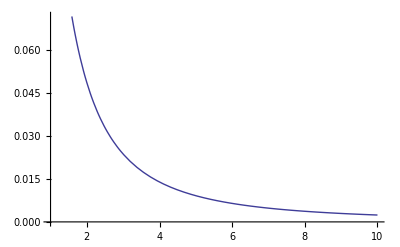

```mathematica
Plot[ dlog[ 2,x],{x,1,10}]
```

```mathematica
Residue[ Zeta[s]^z / z^2,{z,-2}]
```

0

```mathematica
f[100,2,2]
```

283

```mathematica
f[100,2,3]
```

186

```mathematica
f[100,2,3]+2f[100/2,1,3]+f[100/4,0,3]
```

283

```mathematica
tt[a_] := f[100,2,a+1]+2f[100/a,1,a+1]+f[100/a^2,0,a+1]
```

```mathematica
f[n_, k_, a_] := f[n,k,a]=Sum[ f[n/(a+j), k-1, a],{j,0,Floor[n-a]}]; f[n_, 0, a_]:=1 
tt[n_, k_,a_] := Sum[ Binomial[k,j]f[n/a^j,k-j,a+1],{j,0,k}]
ttb[n_, k_,a_] := Sum[ (-1)^j Binomial[k,j]f[n/(a-1)^j,k-j,a-1],{j,0,k}]
```

```mathematica
tt[231,4,2.5]
```

296

```mathematica
ttb[231,4,2.5]
```

296

```mathematica
f[231,4,2.5]
```

296

```mathematica
Limit[f[231,4,z],z->0]
```

$Aborted